# Random graph generation

One sentence description of topic.

Máté Csigi, Jun. 24,  2018

One of the most fascinating insights of network science is that networks taken from entirely different domains are remarkably similar. Understanding the processes responsible for these similarities is one of the primary motivations behind developing graph generating models.

## Generating the graph

One way to start into your exposition is to explain how the basic idea works. If it is a formula, provide the math. If it is an algorithm, describe the steps. If it is an experiment, set up assumptions and provide definitions.

Creating a  random graph based on the Barabasi model:

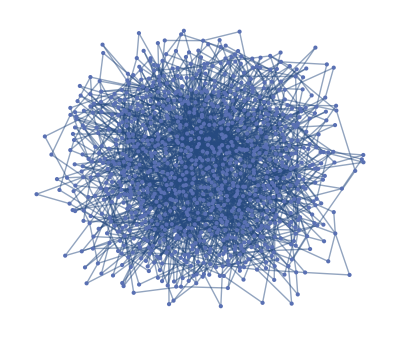

```mathematica
graph=RandomGraph[BarabasiAlbertGraphDistribution[1000,2]]
```

## Degree distribution

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

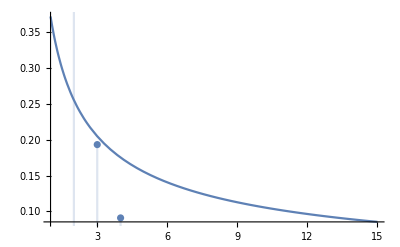

```mathematica
degrees=EmpiricalDistribution[VertexDegree[graph]];
fitDeg=a x^b/.FindFit[Normalize[VertexDegree[graph]],a x^b,{a,b},x];
Show[Plot[fitDeg,{x,1,15}],DiscretePlot[PDF[degrees,k],{k,1,15}]]
```

## Diameter scaling

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

4.99309+0.911553 Log[x]

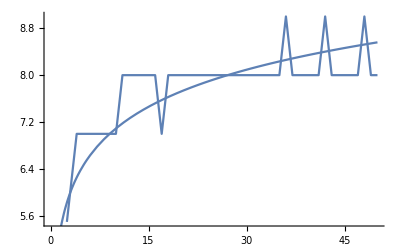

```mathematica
diameters=Table[GraphDiameter[RandomGraph[BarabasiAlbertGraphDistribution[n,2]]],{n,10,5000,100}];
fitDiam=Fit[diameters,{1,Log[x]},x]
Show[ListLinePlot[diameters],Plot[fitDiam,{x,0,50}]]
```

## Rich-club distribution

Name of a related topic for exploration

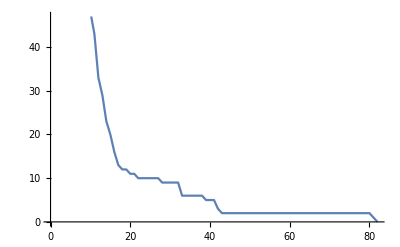

```mathematica
RichClub[g_Graph]:=ListLinePlot[Table[Count[VertexDegree[g],n_/;n>k],{k,1,Max[VertexDegree[g]]}]]
RichClub[graph]
```

## Author contact information

csimate5@gmail.com